```mathematica
(* Solve[{x^2+y^2==y*sin(t)+x*cos(t),x^2+y^2==y*sin((3*t)/2)+x*cos((3*t)/2)},{x,y},Reals] *)

(* Solve x *)
Print[FullSimplify[(cos(t) (sin((3 t)/2))^2+(−sin(t) cos((3 t)/2)−cos(t) sin(t)) sin((3 t)/2)+(sin(t))^2 cos((3 t)/2))/((sin((3 t)/2))^2−2 sin(t) sin((3 t)/2)+(cos((3 t)/2))^2−2 cos(t) cos((3 t)/2)+(sin(t))^2+(cos(t))^2)]];
Print[TrigExpand[(Cos[t]+Cos[3t/2])/2]];
Print[FullSimplify[2 Cos[t/2]^3+Cos[t/2]^2-3/2 Cos[t/2]-1/2 ]];
```

1/2 (Cos[t]+Cos[(3 t)/2])

1/2 Cos[t/2]^2+1/2 Cos[t/2]^3-1/2 Sin[t/2]^2-3/2 Cos[t/2] Sin[t/2]^2

1/2 (Cos[t]+Cos[(3 t)/2])

```mathematica
(* Solve y *)
Print[FullSimplify[−((cos(t) cos((3 t)/2)−(cos(t))^2) sin((3 t)/2)−sin(t) (cos((3 t)/2))^2+cos(t) sin(t) cos((3 t)/2))/((sin((3 t)/2))^2−2 sin(t) sin((3 t)/2)+(cos((3 t)/2))^2−2 cos(t) cos((3 t)/2)+(sin(t))^2+(cos(t))^2)]];
Print[TrigExpand[(Sin[t]+Sin[3t/2])/2]];
Print[FullSimplify[2Sin[t/2] Cos[t/2]^2+Sin[t/2]Cos[t/2]-1/2 Sin[t/2] ]];
```

1/2 (Sin[t]+Sin[(3 t)/2])

Cos[t/2] Sin[t/2]+3/2 Cos[t/2]^2 Sin[t/2]-1/2 Sin[t/2]^3

1/2 (Sin[t]+Sin[(3 t)/2])

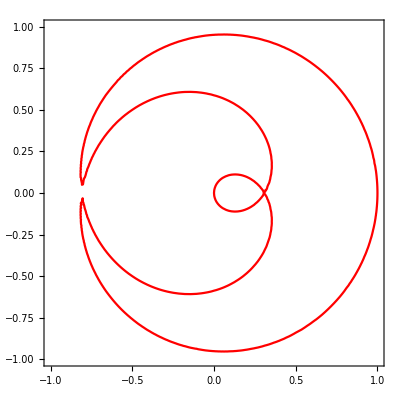

```mathematica
ContourPlot[0==16 y^6+48 x^2 y^4−20 y^4+48 x^4 y^2−40 x^2 y^2+5 y^2+16 x^6−20 x^4+5 x^2−x,{x,-1,1},{y,-1,1}, ContourStyle->Red]
```